```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jedli\OneDrive - NUS High School\Documents\Computing Studies\computed_tomography\logs

```mathematica
data=Import["randomly_masked_sinograms/random_masking_finetuned_5_epochs.csv"];
data=Table[data[[i]],{i,2,Length[data]}];
```

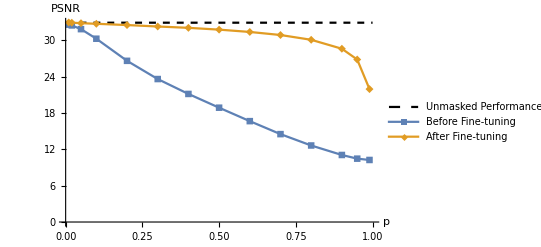

```mathematica
ListPlot[{{{0,data[[2]][[6]]},{1,data[[2]][[6]]}},Map[{#[[2]],#[[5]]}&,data],Map[{#[[2]],#[[6]]}&,data]},AxesLabel->{"p","PSNR"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{Directive[Black,Dashed],ColorData[97,1],ColorData[97,2]},PlotLegends->Placed[{"Unmasked Performance","Before Fine-tuning", "After Fine-tuning"},{0.325,0.2}],Joined->True,PlotMarkers->{None,Automatic,Automatic}]
```

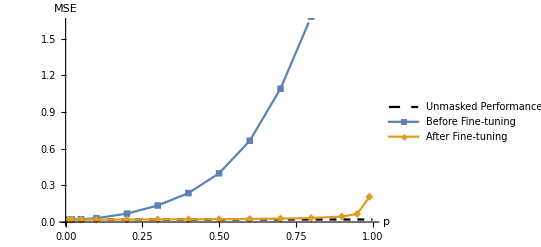

```mathematica
ListPlot[{{{0,data[[2]][[3]]},{1,data[[2]][[3]]}},Map[{#[[2]],#[[3]]}&,data],Map[{#[[2]],#[[4]]}&,data]},AxesLabel->{"p","MSE"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{Directive[Black,Dashed],ColorData[97,1],ColorData[97,2]},PlotLegends->Placed[{"Unmasked Performance","Before Fine-tuning", "After Fine-tuning"},{0.325,0.8}],Joined->True,PlotMarkers->{None,Automatic,Automatic}]
```

```mathematica
data=Import["masked_sinograms/masked_sinograms_finetuned_5_epochs.csv"];
data=Table[data[[i]],{i,2,Length[data]}];
```

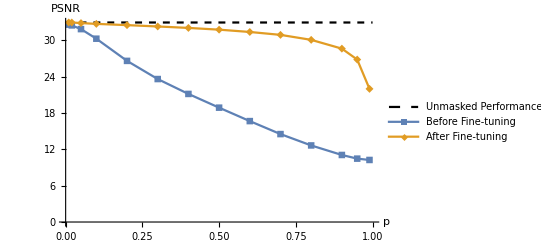

```mathematica
ListPlot[{{{0,data[[2]][[6]]},{1,data[[2]][[6]]}},Map[{#[[2]],#[[5]]}&,data],Map[{#[[2]],#[[6]]}&,data]},AxesLabel->{"p","PSNR"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{Directive[Black,Dashed],ColorData[97,1],ColorData[97,2]},PlotLegends->Placed[{"Unmasked Performance","Before Fine-tuning", "After Fine-tuning"},{0.325,0.2}],Joined->True,PlotMarkers->{None,Automatic,Automatic}]
```

```mathematica
data=Import["low_dose/low_dose_finetuned_5_epochs.csv"];
data=Table[data[[i]],{i,2,Length[data]}];
```

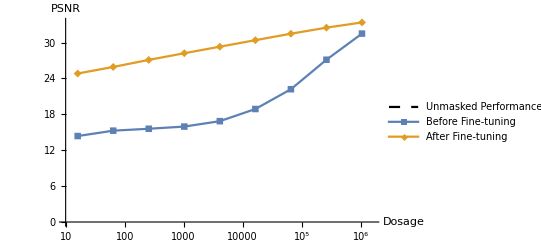

```mathematica
ListLogLinearPlot[{{{0,data⟦2⟧⟦6⟧},{10^8,data⟦2⟧⟦6⟧}},({#1⟦2⟧,#1⟦5⟧}&)/@data,({#1⟦2⟧,#1⟦6⟧}&)/@data},AxesLabel->{"Dosage","PSNR"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{Directive[Black,Dashed],ColorData[97,1],ColorData[97,2]},PlotLegends->Placed[{"Unmasked Performance","Before Fine-tuning","After Fine-tuning"},{0.325,0.2}],Joined->True,PlotRange->{{10,10^6.2},All},PlotMarkers->{None,Automatic,Automatic}]
```

```mathematica
data=Import["poca_dosage_data.csv"]
```

{{100,2.22675},{200,1.86163},{500,1.49393},{700,1.38557},{1000,1.26125},{2000,1.14453},{5000,1.08401},{7000,1.06955},{10000,1.05937},{20000,1.05095}}

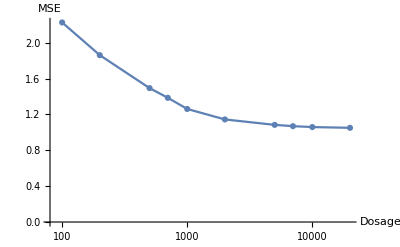

```mathematica
ListLogLinearPlot[data,AxesLabel->{"Dosage","MSE"},AxesStyle->Directive[Black,Thickness[0.003]],Joined->True,PlotMarkers->Automatic]
```